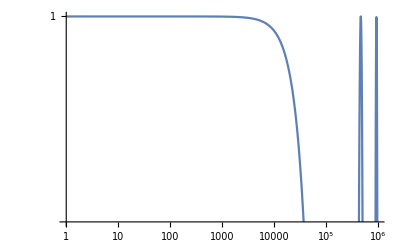

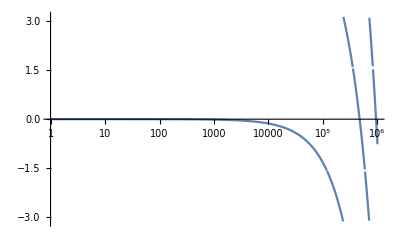

```mathematica
c=3 10^8;
L=4 10^3;
LogLogPlot[Re[Exp[- (ⅈ Ω L)/c]],{Ω,1,10^6},PlotLegends->"Expressions"]
LogLinearPlot[Arg[Exp[ (-ⅈ Ω L)/c]],{Ω,1,10^6},PlotLegends->"Expressions",PlotRange->{-π,π}]
```

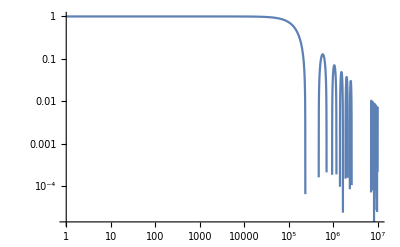

```mathematica
LogLogPlot[Sinc[(Ω L)/c],{Ω,1,10^7},PlotRange->All]
```

```mathematica
Manipulate[Plot[{Sin[Ω x],(-Cos[Ω x])/Ω,-Cos[Ω x],Ω Sin[Ω x]},{x,0,2π},PlotLegends->"Expressions",PlotRange->{-2,2}],{{Ω,1},1/2,3/2}]
```